```mathematica
(* https://mathematica.stackexchange.com/questions/261561/generating-1-f-noise *)
(* Timmer Konig 1995 *)
(* astrochron/R/FUNCTION-makeNoise_v3.R *)
```

```mathematica
nn=2^22(*Number of spectral points*)
S[f_]:=1/f;
Timing[
s1=Table[If[f!=nn/2,
(RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]]),
RandomVariate[NormalDistribution[]]]*
 Sqrt[S[f]/2],{f,1,nn/2 }];
s2=Join[{0},s1,Reverse[Conjugate[s1[[1;;-2]]]]];
]
pwr=s2.Conjugate[s2];
norm=1/Sqrt[pwr];
```

4194304

{22.6094,Null}

{0.155478,Null}

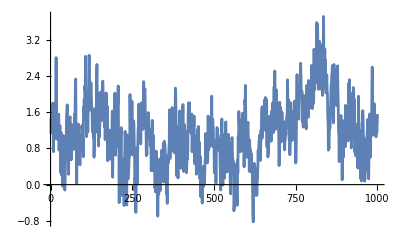

```mathematica
Timing[if=InverseFourier[s2,FourierParameters->{-1,-1}];]
l=Chop[norm if];
ListLinePlot[Take[l,UpTo[1000]]]
```

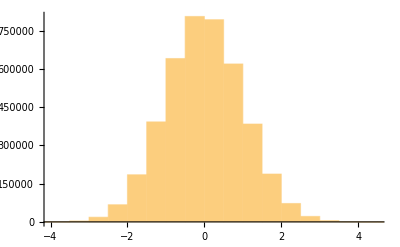

1.14492×10^-16

1.

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.891585},{2,0.839707},{3,0.815204},{4,0.795287},{5,0.781332},{6,0.768815},{7,0.759117},{8,0.750166},{9,0.742559},{10,0.73564},{11,0.729611},{12,0.723762},{13,0.718628},{14,0.713622},{15,0.709106},{16,0.704755},{17,0.700794},{18,0.696984},{19,0.693577},{20,0.690116},{21,0.686913},{22,0.683814},{23,0.680924},{24,0.678156},{25,0.675429},{26,0.673051},{27,0.670557},{28,0.668281},{29,0.666062},{30,0.66385},{31,0.661648},{32,0.659515},{33,0.657511},{34,0.655626},{35,0.653684},{36,0.651841},{37,0.650085},{38,0.648308},{39,0.646534},{40,0.644895},{41,0.6434},{42,0.641742},{43,0.640221},{44,0.638638},{45,0.637341},{46,0.635914},{47,0.634512},{48,0.633151},{49,0.631827},{50,0.630542},{51,0.629131},{52,0.627842},{53,0.626593},{54,0.625374},{55,0.624122},{56,0.6231},{57,0.62189},{58,0.620986},{59,0.61998},{60,0.618831},{61,0.617649},{62,0.616555},{63,0.615543},{64,0.614455},{65,0.61339},{66,0.61231},{67,0.611146},{68,0.610217},{69,0.609453},{70,0.608582},{71,0.607715},{72,0.606787},{73,0.605913},{74,0.605008},{75,0.604022},{76,0.603412},{77,0.60261},{78,0.60181},{79,0.6009},{80,0.600031},{81,0.599394},{82,0.598515},{83,0.597789},{84,0.597056},{85,0.596094},{86,0.595257},{87,0.594489},{88,0.593805},{89,0.59311},{90,0.592488},{91,0.591872},{92,0.590997},{93,0.590299},{94,0.589637},{95,0.589016},{96,0.588398},{97,0.587678},{98,0.586859},{99,0.586293},{100,0.585622}}

{a→0.886608,b→0.0654491}

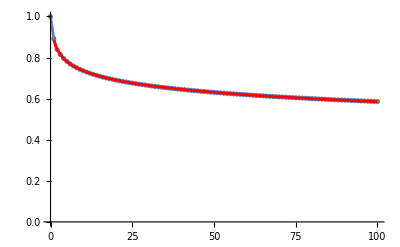

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

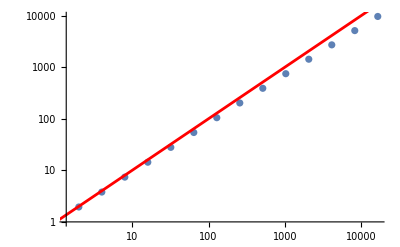

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

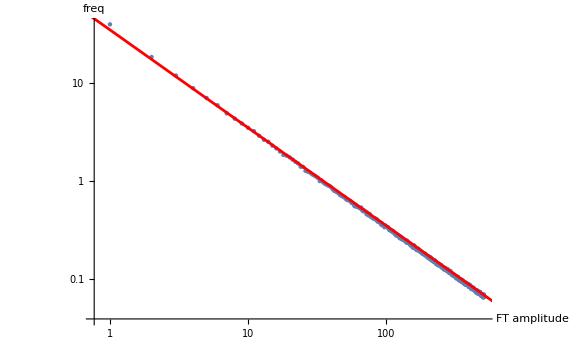

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"FT amplitude","freq"},LabelStyle->Larger];
pft2=LogLogPlot[{35/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```